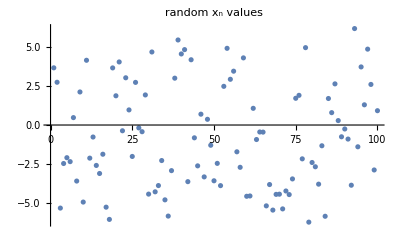

```mathematica
On[Assert]
n = 100;
testdata = RandomReal[{-2*π, 2*π}, n];

noisify[data_] := data + (.1 * Normal[
RandomFunction[
WhiteNoiseProcess[], 
{0,Dimensions[data][[1]]-1}]][[1]][[All,2]] );

trainingfunction[x_] := noisify[LogisticSigmoid[x]] ;

ListPlot[testdata, PlotLabel->"random x_n values"]
```

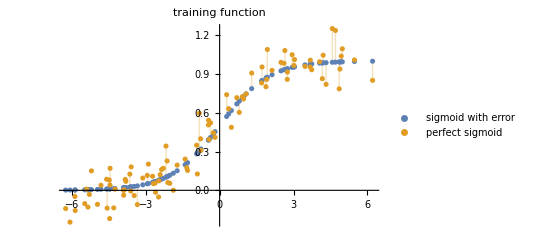

```mathematica
y = Evaluate[trainingfunction[testdata]];
yclean = Evaluate[LogisticSigmoid[testdata]];
plotdata = Transpose@{testdata,y};
plotdataclean = Transpose@{testdata, yclean};
ListPlot[{plotdataclean,plotdata}, PlotLabel->"training function",  Filling->{2 -> {1}}, PlotLegends-> Placed[{"sigmoid with error", "perfect sigmoid"}, Right]]
```